# Neural Networks

## NetTrain

1. Define a single-layer neural network that takes in scalar numeric values and produces scalar numeric values:

```mathematica
net=DotPlusLayer[1, "Input"->"Scalar", "Output"-> "Scalar"]
```

DotPlusLayer[…]

```mathematica
trained = NetTrain[net, {1->8, 2->19, 3->28, 4-> 37}]
```

None

```mathematica
trained[2.4]
```

22.04

```mathematica
trained[{1,2,3,4}]
```

{8.60003,18.2,27.8,37.4}

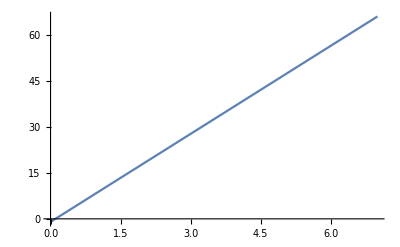

```mathematica
Plot[trained[x],{x,0,7}]
```

2. Define a network that takes in scalar numeric values and produces vectors of length two that are used as probabilities for the classes True and False:

```mathematica
net= NetChain[{DotPlusLayer[2], SoftmaxLayer[2]},
	"Input"->"Scalar", "Output"-> NetDecoder[{"Class", {True, False}}]]
```

NetChain[]

```mathematica
trained = NetTrain[net, {1 -> False, 2-> False, 3-> True, 4-> True}]
```

NetChain[]

```mathematica
trained [3.5]
```

True

```mathematica
trained[Range[10]]
```

{False,False,True,True,True,True,True,True,True,True}

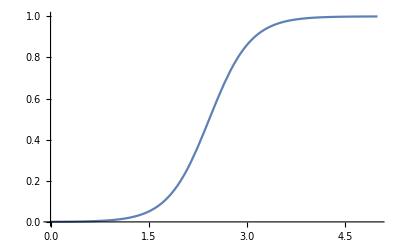

```mathematica
Plot[trained[x,{"Probability", True}], {x, 0, 5}]
```

```mathematica
net = NetChain[{32, Tanh, 1}, "Input" ->2, "Output"->"Scalar"]
```

NetChain[]

3. Define a three-layer network that takes in vectors of length two and produces scalar numeric values:

NetChain[]

```mathematica
trainingData = Flatten[Table[{x,y}->x*y,{x,-1,1,.005}, {y, -1,1,.005}]];
```

```mathematica
trained = NetTrain[net, trainingData, BatchSize->1024]
```

NetChain[]

```mathematica
Plot3D[trained[{x,y}],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

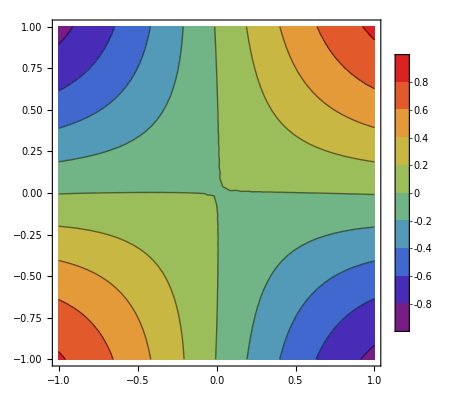

```mathematica
ContourPlot[trained[{x,y}],{x,-1,1},{y,-1,1},
	ColorFunction->"Rainbow", PlotLegends->Automatic]
```

## Loss Specifications

Train a simple net using MeanSquaredLossLayer

```mathematica
net = DotPlusLayer["Input"-> "Scalar", "Output"-> "Scalar"];
data = {1->1.9, 2->4.1, 3-> 6.0, 4-> 8.1};
trained = NetTrain[net, data]
```

None

```mathematica
trained[Range[4]]
```

{1.95001,4.,6.05,8.09999}

```mathematica
loss = MeanAbsoluteLossLayer["Target"-> "Scalar"]
```

MeanAbsoluteLossLayer[…]

```mathematica
loss[<|"Input"->5.0, "Target" -> 3.0|>]
```

2.

```mathematica
data = {1 -> 1.9, 2 -> 4.1, 3 -> 6.0, 4 -> 8.1};
trained = NetTrain[net, data, loss]
```

None

```mathematica
trained[Range[4]]
```

{1.89997,3.96671,6.03346,8.1002}

## Options

1. BatchSize

### ?

```mathematica
trainingData = 
  RandomReal[1, {10000, 4}] -> RandomReal[1, {10000, 4}];
net = NetChain[{DotPlusLayer[8], DotPlusLayer[4]}, "Input" -> 4];
NetTrain[net, trainingData, BatchSize -> 512, 
   MaxTrainingRounds -> 20]; // AbsoluteTiming
```

{0.254998,Null}

MaxTrainingRounds

```mathematica
trainingData = 
  RandomReal[1, {10000, 4}] -> RandomReal[1, {10000, 4}];
net = NetChain[{8, 4}, "Input" -> 4];
NetTrain[net, trainingData, MaxTrainingRounds -> 1]
```

NetChain[]

## Method

1. Stochastic Gradient Decent

```mathematica
dotPlus = DotPlusLayer[1,"Input"-> "Scalar", "Output"-> "Scalar"]
```

DotPlusLayer[…]

```mathematica
data = {1 -> 2.2, 2 -> 3.8, 3 -> 6.4, 4 -> 9.1};
```

```mathematica
net = NetTrain[dotPlus, data, Method -> "StochasticGradientDescent"]
```

None

```mathematica
net = NetTrain[dotPlus, data, 
  Method -> {"StochasticGradientDescent", 
    "InitialLearningRate" -> 0.1}]
```

None

2. Use regularization to prevent overfitting. Create synthetic training data based on a Gaussian curve:

```mathematica
data = Table[
   x -> Exp[-x^2] + RandomVariate[NormalDistribution[0, .15]], {x, -3,
     3, .2}];
```

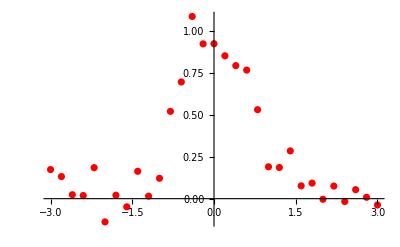

```mathematica
plot = ListPlot[List @@@ data, PlotStyle -> Red]
```

## 0108 Youtube Hands-on with Neural Networks https://www.youtube.com/watch?v=JBBLPUydA0k

## Layers

Layer Types and when to use them

### DotPlusLayer

```mathematica
dot = DotPlusLayer[2,5]
```

DotPlusLayer[…]

```mathematica
NetExtract[dot,"Weights"]
```

Automatic

#### ? Initialize value, 每次运算前都需要Initialize么？

```mathematica
dot = NetInitialize[dot]
```

None

```mathematica
NetExtract[dot,"Weights"]
```

{{0.100565,-0.184286,0.302927,0.647902,0.388504},{0.60376,0.0185085,-0.403516,-0.367791,0.528902}}

### ElementwiseLayer

```mathematica
elem = ElementwiseLayer[Tanh, "Input"-> {3,5}]
```

ElementwiseLayer[…]

#### Use the DotPlusLayer below, initialize it, and check that the answer on the vector{0.,0.2,.1} is the same as M{0.,0.2,.1}+b, where M is the weights matrix and b is the bias.

```mathematica
dotp = DotPlusLayer[5, "Input"-> 3]
```

DotPlusLayer[…]

```mathematica
dotp = NetInitialize@DotPlusLayer[5, "Input"-> 3];
dotp@{3,4,5}
```

{-5.87672,4.40698,-4.0858,-3.89332,3.72982}

```mathematica
NetExtract[dotp,"Weights"]
```

{{-0.222752,-0.798017,-0.403279},{0.290179,0.727842,0.125015},{-0.49786,-0.291949,-0.284886},{-0.308871,0.120017,-0.689356},{-0.620511,0.737932,0.527927}}

```mathematica
NetExtract[dotp,"Biases"]
```

{0.,0.,0.,0.,0.}

#### ReshapeLayer and FlattenLayer Tensor vector

```mathematica
reshape = ReshapeLayer[{2,2}]
```

ReshapeLayer[…]

```mathematica
reshape[{1,2,3,4}]
```

{{1.,2.},{3.,4.}}

```mathematica
flat = FlattenLayer[]
```

FlattenLayer[…]

```mathematica
flat@{{1,2,3,4},{2,3,3,2}}
```

{1.,2.,3.,4.,2.,3.,3.,2.}

### LostLayer

#### MeanSquaredLossLayer

```mathematica
data= <|"Input"-> {1,2}, "Target"-> {4,5}|>
```

<|Input→{1,2},Target→{4,5}|>

```mathematica
MeanSquaredLossLayer[]@data
```

9.

```mathematica
f = Mean[(#Input- #Target)^2]&
```

Mean[(#Input-#Target)^2]&

```mathematica
f@data
```

9

## Containers

NetChain and NetGraph

```mathematica
NetChain[{Ramp, ConvolutionLayer[64, {3,3}], PoolingLayer[]}]
```

NetChain[]

```mathematica
NetGraph[{Ramp, ConvolutionLayer[64, {3,3}], PoolingLayer[]},{1-> 2, 2->3}]
```

NetGraph[]

```mathematica
NetGraph[<|"ramp1"-> Ramp, "conv1"-> ConvolutionLayer[64, {3,3}], "pool1"-> PoolingLayer[]|>,
		{"ramp1"-> "conv1", "conv1"->"pool1"}]
```

NetGraph[]

```mathematica
NetGraph[{Ramp, LogisticSigmoid, CatenateLayer[]},{1-> 2, {1,2}->3}]
```

NetGraph[]

NetTrain

#### Define and train a net to add three numbers:

```mathematica
data = (#-> {Plus@@ #}) & /@ RandomReal[1000, {100, 3}];
```

```mathematica
net = NetChain[{DotPlusLayer[1]}, "Input"-> 3]
```

NetChain[]

```mathematica
net = NetTrain[net, data, Method->"ADAM"]
```

NetChain[]

```mathematica
net@{200, 300, 120}
```

```mathematica
NetExtract[NetExtract[net, 1], "Weights"]
```

{{0.999917,0.999943,0.999942}}

#### Define and train a net to add three numbers using both MeanSquaredLayer and MeanAbosoluteLossLayer:

```mathematica
NetGraph[<|"dot"-> DotPlusLayer[1]>, 
{NetPort["Input"]-> "dot", "Target1"}
```

```mathematica
data = (#-> {Plus@@ #}) & /@ RandomReal[1000, {100, 3}];
```